# The Dragon Curve

Adam Rumpf, 5/6/2016

## Introduction

A dragon curve is a type of fractal curve that can be recursively defined by beginning with a line segment and then iteratively appending a copy of the previous generation to itself, rotated by 90 degrees. The construction of the nth generation can be visualized by folding a thin strip of paper in half n times and then unfolding it so that each crease opens at a 90 degree angle. The first few generations do not look very interesting, but the curve quickly grows into an intricate fractal spiral.

An equivalent construction involves beginning with a line segment and then iteratively replacing each line segment with an L-shaped segment (as if the L forms the legs of a 45-45-90 triangle with the previous line segment as the hypotenuse), and alternating whether the new lines are drawn above or below the previous segment. This is the method used by the functions below.

The main function defined in this Notebook is dragon[], which accepts a single nonnegative integer argument. The function produces a graphics object displaying the specified generation of dragon curve.

## Code

### Initialization

```mathematica
displayout[c_,d_,l_]:=Module[{lines,temp,newl},
If[d[[1]]=="ne"||d[[1]]=="se"||d[[1]]=="sw"||d[[1]]=="nw",
newl=l/(2 √2),
newl=l/2;
];
lines=ConstantArray[0,2Length[c]];
For[i=1,i≤Length[c],i++,
Switch[d[[i]],
"n",
temp={c[[i]]+{0,-newl},c[[i]]+{0,newl}},
"ne",
temp={c[[i]]+{-newl,-newl},c[[i]]+{newl,newl}},
"e",
temp={c[[i]]+{-newl,0},c[[i]]+{newl,0}},
"se",
temp={c[[i]]+{-newl,newl},c[[i]]+{newl,-newl}},
"s",
temp={c[[i]]+{0,newl},c[[i]]+{0,-newl}},
"sw",
temp={c[[i]]+{newl,newl},c[[i]]+{-newl,-newl}},
"w",
temp={c[[i]]+{newl,0},c[[i]]+{-newl,0}},
"nw",
temp={c[[i]]+{newl,-newl},c[[i]]+{-newl,newl}}
];
lines[[2i-1;;2i]]=temp;
];
Graphics[Line[lines]]
]
```

```mathematica
iterate[c_,d_,l_]:=Module[{outc,outd,outl,tempc,tempd,newl,cw=-1},
outl=l/√2;
outc=ConstantArray[0,2Length[c]];
outd=ConstantArray[0,2Length[d]];
If[d[[1]]=="ne"||d[[1]]=="se"||d[[1]]=="sw"||d[[1]]=="nw",
newl=outl/2,
newl=outl/(2 √2);
];
For[i=1,i≤Length[c],i++,
cw*=-1;
Switch[d[[i]],
"n",
If[cw==1,
tempc={c[[i]]+{newl,-newl},c[[i]]+{newl,newl}};
tempd={"ne","nw"},
tempc={c[[i]]+{-newl,-newl},c[[i]]+{-newl,newl}};
tempd={"nw","ne"};
],
"ne",
If[cw==1,
tempc={c[[i]]+{0,-newl},c[[i]]+{newl,0}};
tempd={"e","n"},
tempc={c[[i]]+{-newl,0},c[[i]]+{0,newl}};
tempd={"n","e"};
],
"e",
If[cw==1,
tempc={c[[i]]+{-newl,-newl},c[[i]]+{newl,-newl}};
tempd={"se","ne"},
tempc={c[[i]]+{-newl,newl},c[[i]]+{newl,newl}};
tempd={"ne","se"};
],
"se",
If[cw==1,
tempc={c[[i]]+{-newl,0},c[[i]]+{0,-newl}};
tempd={"s","e"},
tempc={c[[i]]+{0,newl},c[[i]]+{newl,0}};
tempd={"e","s"};
],
"s",
If[cw==1,
tempc={c[[i]]+{-newl,newl},c[[i]]+{-newl,-newl}};
tempd={"sw","se"},
tempc={c[[i]]+{newl,newl},c[[i]]+{newl,-newl}};
tempd={"se","sw"};
],
"sw",
If[cw==1,
tempc={c[[i]]+{0,newl},c[[i]]+{-newl,0}};
tempd={"w","s"},
tempc={c[[i]]+{newl,0},c[[i]]+{0,-newl}};
tempd={"s","w"};
],
"w",
If[cw==1,
tempc={c[[i]]+{newl,newl},c[[i]]+{-newl,newl}};
tempd={"nw","sw"},
tempc={c[[i]]+{newl,-newl},c[[i]]+{-newl,-newl}};
tempd={"sw","nw"};
],
"nw",
If[cw==1,
tempc={c[[i]]+{newl,0},c[[i]]+{0,newl}};
tempd={"n","w"},
tempc={c[[i]]+{0,-newl},c[[i]]+{-newl,0}};
tempd={"w","n"};
];
];
outc[[2i-1;;2i]]=tempc;
outd[[2i-1;;2i]]=tempd;
];
{outc,outd,outl}
]
```

```mathematica
display[c_,d_,l_]:=Module[{lines,temp,newl},
If[d[[1]]=="ne"||d[[1]]=="se"||d[[1]]=="sw"||d[[1]]=="nw",
newl=l/(2 √2),
newl=l/2;
];
lines=ConstantArray[0,2Length[c]];
For[i=1,i≤Length[c],i++,
Switch[d[[i]],
"n",
temp={c[[i]]+{0,-newl},c[[i]]+{0,newl}},
"ne",
temp={c[[i]]+{-newl,-newl},c[[i]]+{newl,newl}},
"e",
temp={c[[i]]+{-newl,0},c[[i]]+{newl,0}},
"se",
temp={c[[i]]+{-newl,newl},c[[i]]+{newl,-newl}},
"s",
temp={c[[i]]+{0,newl},c[[i]]+{0,-newl}},
"sw",
temp={c[[i]]+{newl,newl},c[[i]]+{-newl,-newl}},
"w",
temp={c[[i]]+{newl,0},c[[i]]+{-newl,0}},
"nw",
temp={c[[i]]+{newl,-newl},c[[i]]+{-newl,newl}}
];
lines[[2i-1;;2i]]=temp;
];
Show[Graphics[Line[lines]]]
]
```

```mathematica
dragon[n_]:=Module[{c,d,l},
c={{1/2,0}};
d={"e"};
l=1;
For[k=1,k≤n,k++,
{c,d,l}=iterate[c,d,l];
];
display[c,d,l]
]
```

### Demonstration

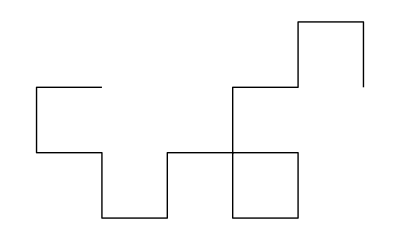

```mathematica
(* Draw 4th generation dragon curve. *)
dragon[4]
```

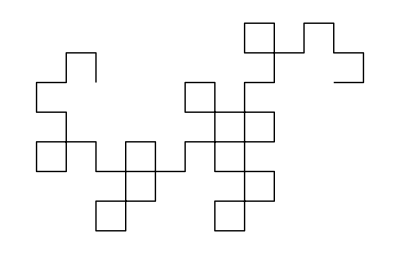

```mathematica
(* Draw 6th generation dragon curve. *)
dragon[6]
```

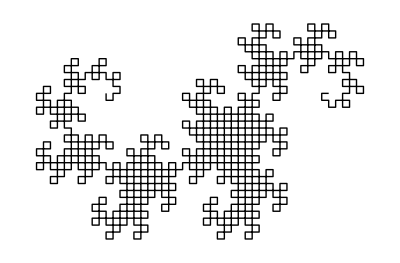

```mathematica
(* Draw 10th generation dragon curve. *)
dragon[10]
```

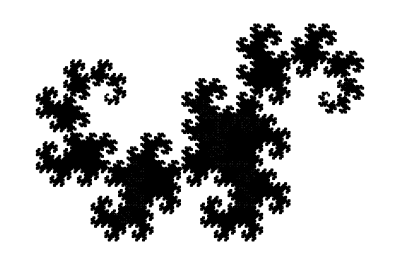

```mathematica
(* Draw 14th generation dragon curve. *)
dragon[14]
```

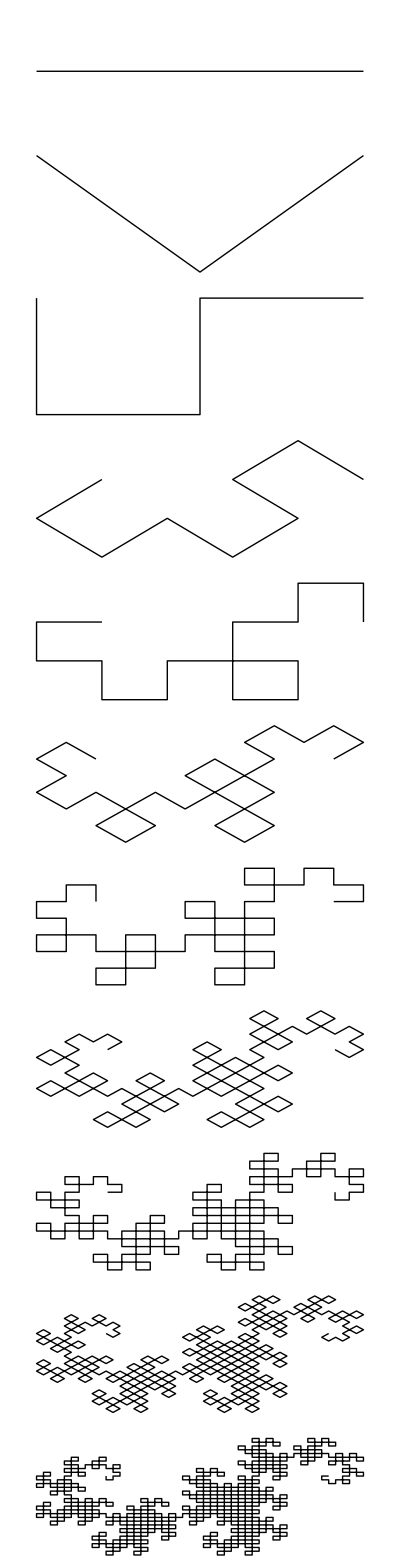

```mathematica
(* Produce a table of each dragon curve from generations 0 to 15. *)
TableForm[Table[dragon[n],{n,0,10}]]
```